```mathematica
(*L,T,a*)
a=1;
LT={{2000,100,a},{2000,300,a},{2000,1000,a},{2000,3000,a},{2000,10000,a},{2000,30000,a},{2000,100000,a},{2000,300000,a},{2000,1000000,a},{2000,3000000,a}};
data=Table[ReadList[StringJoin["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\P_L",ToString[LT[[i,1]]],"OT",ToString[LT[[i,2]]],"_u120t0100.txt"],Number],{i,1,Length[LT]}];
Map[Length,data]
binr=Table[BinCounts[data[[i]],{0,Max[data[[i]]]+1,LT[[i,3]]}],{i,1,Length[LT]}];
datar=Table[{j*LT[[i,3]],binr[[i,j]]/(j*LT[[i,3]])},{i,1,Length[LT]},{j,3,Length[binr[[i]]]}];
```

{12000,12000,12000,12000,12000,12000,12000,12000,12000,8000}

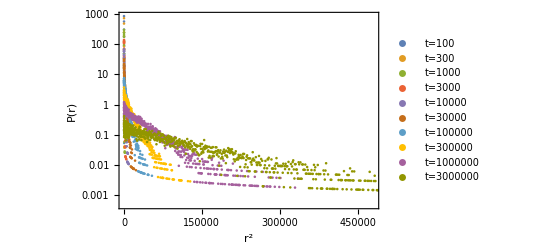

```mathematica
ListPlot[Map[{(#[[1]])^2,#[[2]]}&,datar,{2}],ScalingFunctions->"Log",PlotLegends->Table[StringJoin["t=",ToString[LT[[i,2]]]],{i,1,Length[LT]}],Frame->True,FrameLabel->{"r^2","P(r)"}]
```

{4000,4000,4000,4000,4000,4000,4000,4000,4000}

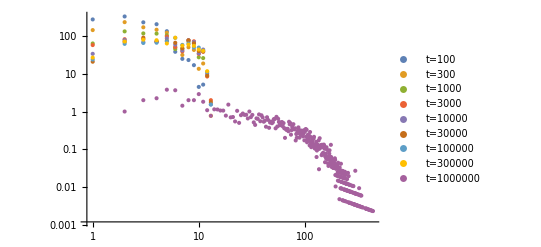

```mathematica
(*ScalingFunctions->{"Log","Log"},Plot[{Exp[f100],Exp[f500],Exp[f1000],Exp[f5000],Exp[f10000],Exp[f50000],Exp[f100000]},{x,0,1000},ScalingFunctions->{"Log","Log"},PlotLegends->{"-16±1","-15±1","-15±1","-13±1","-13±1","-13±1","-11±1"}]*)
a=1;
L=4000;
LT={{L,100,a},{L,300,a},{L,1000,a},{L,3000,a},{L,10000,a},{L,30000,a},{L,100000,a},{L,300000,a},{L,1000000,a}};
data=Table[ReadList[StringJoin["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\P_L",ToString[LT[[i,1]]],"OT",ToString[LT[[i,2]]],"_u120t0100.txt"],Number],{i,1,Length[LT]}];
Map[Length,data]
binr=Table[BinCounts[data[[i]],{0,Max[data[[i]]]+1,LT[[i,3]]}],{i,1,Length[LT]}];
datar=Table[{j*LT[[i,3]],binr[[i,j]]/(j*LT[[i,3]])},{i,1,Length[LT]},{j,1,Length[binr[[i]]]}];
ListPlot[datar,ScalingFunctions->{"Log","Log"},PlotLegends->Table[StringJoin["t=",ToString[LT[[i,2]]]],{i,1,Length[LT]}]]
```